# Entrelazamiento y separabilidad de estados puros en subespacios bidimensionales de sistemas bipartitos de 2 y más qubits

Por:  Subadra Echeverria

## 2 qubits

### Estados separables

#### Funciones

Consultar la documentación de las funciones en la secciones 2.4  y 2.5 del trabajo de tesis.

```mathematica
OrthonormalBasis[n_]:=Orthogonalize[Table[RandomComplex[{-1+I,1+I}],2,2^n]]
Partial[ρ_,Q_]:=Module[{n,Ilist,A,Positions,VectorsBasis,VB2,VB3,VB4},
n=Log[2,Dimensions[ρ][[1]]];(*número de qubits que conforman al estado ρ*)
Ilist=ConstantArray[IdentityMatrix[2],n];(*construye una lista con n matrices identidad de 2x2 para luego solo sustituir a las que estén asociadas a los qubits de la lista Q por los vectores base y así aplicar ρ para obtener la traza parcial*)
Positions=Tuples[{1,2},Length[Q]];(*índices de las combinaciones posibles de los estados base|0>y|1>que serán necesarios para el número de qubits en Q*)VectorsBasis=Table[IdentityMatrix[2][[#]]&@Positions[[i]],{i,1,Length[Positions]}];(*estados|0>,|1>necesarios para calcular la traza parcial*)
VB2=Table[{#}&/@VectorsBasis[[i]],{i,1,Length[VectorsBasis]}];
VB3=Flatten[Map[Thread[{Q->#}]&,VB2]];(*indicadores que se usarán para posicionar a los estados base en la lista Ilist,considerando sobre qué qubits se va a trazar*)VB4=Table[Thread[VB3[[i]]],{i,1,Length[VB3]}];
A=Table[KroneckerProduct[##]&@@ReplacePart[Ilist,VB4[[i]]],{i,1,Length[VB4]}];(*construye a las matrices que se van a aplicar sobre ρ para obtener a la traza parcial*)Sum[A[[i]].ρ.Transpose[A[[i]]],{i,1,Length[A]}]]

ReducedDensityMatrix[ρ_,Qubits_]:=Module[{n,Ilist,A,Positions,VectorsBasis,VB2,VB3,VB4},
n=Log[2,Dimensions[ρ][[1]]];(*número de qubits que conforman al estado ρ*)
Ilist=ConstantArray[IdentityMatrix[2],n];(*construye una lista con n matrices identidad de 2x2 para luego solo sustituir a las que estén asociadas a los qubits de la lista Qubits por los vectores base y así aplicar ρ para obtener la traza parcial*)Positions=Tuples[{1,2},Length[Qubits]];(*índices de las combinaciones posibles de los estados base|0>y|1>que serán necesarios para el número de qubits en Qubits*)VectorsBasis=Table[IdentityMatrix[2][[#]]&@Positions[[i]],{i,1,Length[Positions]}];(*estados|0>,|1>necesarios para calcular la traza parcial*)
VB2=Table[{#}&/@VectorsBasis[[i]],{i,1,Length[VectorsBasis]}];
VB3=Flatten[Map[Thread[{Qubits->#}]&,VB2]];(*indicadores que se usarán para posicionar a los estados base en la lista Ilist,considerando sobre qué qubits se va a trazar*)VB4=Table[Thread[VB3[[i]]],{i,1,Length[VB3]}];
A=Table[KroneckerProduct[##]&@@ReplacePart[Ilist,VB4[[i]]],{i,1,Length[VB4]}];(*construye a las matrices que se van a aplicar sobre ρ para obtener a la traza parcial*)Sum[A[[i]].ρ.Transpose[A[[i]]],{i,1,Length[A]}]]

PurityOfSubsystemA[v1_,v2_,θ_,ϕ_]:=Module[{ψ,ρ,ρA},
ψ=Cos[θ/2] v1+Exp[I ϕ] Sin[θ/2] v2;(*Construye el estado puro*)
ρ=Transpose[{ψ}].Conjugate[{ψ}];(*Matriz densidad del estado ψ*)
ρA=ReducedDensityMatrix[ρ,{2}];(*Matriz densidad reducida*)
Chop[FullSimplify[Tr[MatrixPower[ρA,2]],Element[{θ,ϕ},Reals]]] (*Pureza de ρA*)]

MaximumPurity[v1_,v2_]:=Module[{M,dev,sol,d,data,secdθ,secdϕ,secdθϕ,delta,m,max,points,θ,ϕ},dev={FullSimplify[Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],θ],Element[{θ,ϕ},Reals]]],FullSimplify[Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],ϕ],Element[{θ,ϕ},Reals]]]};
M=NMaximize[{PurityOfSubsystemA[v1,v2,θ,ϕ],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]];
(*Busca los puntos {θ,ϕ} donde la derivada es cero empezando en {θ=θ0,ϕ=ϕ0}*)sol[θ0_,ϕ0_]:={θ,ϕ}/.FindRoot[{dev[[1]]==0,dev[[2]]==0},{θ,θ0,0,Pi},{ϕ,ϕ0,0,2 Pi}];
d=0.5;
data=Table[sol[θ0,ϕ0],{θ0,0,Pi,d},{ϕ0,0,2 Pi,0.5}]//Flatten[#,1]&//DeleteDuplicates@Chop[#]&//Quiet;(*Tabla con los valores {θ,ϕ} en donde la derivada es cero,para distintos puntos {θ0,ϕ0} de partida*)secdθ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,2}]];(*segunda derivada parcial en θ*)
secdϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{ϕ,2}]];(*segunda derivada parcial en ϕ*)
secdθϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,1},{ϕ,1}]];(*segunda derivada en θ,ϕ*)
delta[θ_,ϕ_]:=secdθ[θ,ϕ] secdϕ[θ,ϕ]-secdθϕ[θ,ϕ]^2;(*determinante de la matriz Jacobiana*)
m=Select[data,delta@@#>0&&secdθ@@#<0&];
(*Elimina puntos repetidos que tengan una diferencia menor a 10^-30*,Primer Intento*)
max=DeleteDuplicates[m,Norm[#1-#2]<10^-13&];
(*elimina los puntos en la frontera DeleteCases[max,{x_,y_}/;0==y||y==2 Pi||PurityOfSubsystemA[v1,v2,x,y]<M]*)points=DeleteCases[max,{x_,y_}/;PurityOfSubsystemA[v1,v2,x,y]<M];
If[Length[points]>0,{points,PurityOfSubsystemA[v1,v2,points[[1,1]],points[[1,2]]]},{}]]

AnalyticalSeparableStates[v1_,v2_]:=Module[{α0,α1,α2,α3,β0,β1,β2,β3,Bp1,Bp2,Bp3,SOL1,SOL2,A1,A2,B1,B2},α0=v1[[1]];
α1=v1[[2]];
α2=v1[[3]];
α3=v1[[4]];
β0=v2[[1]];
β1=v2[[2]];
β2=v2[[3]];
β3=v2[[4]];
Bp1=-(β0 α3+α0 β3-α1 β2-α2 β1);(*término-b*)
Bp2=Sqrt[(β0 α3+α0 β3-α1 β2-α2 β1)^2-4 (β0 β3-β1 β2) (α0 α3-α1 α2)];(*término Sqrt[b^2-4ac]*)
Bp3=2 (β0 β3-β1 β2);(*término 2a*)
SOL1=(Bp1+Bp2)/Bp3;(*Primer valor de B'*)
SOL2=(Bp1-Bp2)/Bp3;(*Segundo valor de B'*)
A1=1/Sqrt[1+Norm[SOL1]^2];
B1=SOL1/Sqrt[1+Norm[SOL1]^2];
A2=1/Sqrt[1+Norm[SOL2]^2];
B2=SOL2/Sqrt[1+Norm[SOL2]^2];
{{A1,B1},{A2,B2},{A1 v1+B1 v2,A2 v1+B2 v2}}]

SeparableStatesWith1QStates[v1_,v2_]:=Module[{α0,α1,α2,α3,β0,β1,β2,β3,A1,A2,B1,B2,δ11,δ12,γ11,γ12,s1,s2,S1,S2,K01K02,K11K12},α0=v1[[1]];
α1=v1[[2]];
α2=v1[[3]];
α3=v1[[4]];
β0=v2[[1]];
β1=v2[[2]];
β2=v2[[3]];
β3=v2[[4]];
A1=AnalyticalSeparableStates[v1,v2][[1,1]];
B1=AnalyticalSeparableStates[v1,v2][[1,2]];
A2=AnalyticalSeparableStates[v1,v2][[2,1]];
B2=AnalyticalSeparableStates[v1,v2][[2,2]];
δ11=((A1 α1+B1 β1)/(A1 α0+B1 β0)+(A1 α3+B1 β3)/(A1 α2+B1 β2))/2;(*delta' para A1 y B1*)
δ12=((A2 α1+B2 β1)/(A2 α0+B2 β0)+(A2 α3+B2 β3)/(A2 α2+B2 β2))/2; (*delta' para A2 y B2*)
γ11=((A1 α2+B1 β2)/(A1 α0+B1 β0)+(A1 α3+B1 β3)/(A1 α1+B1 β1))/2;(*gamma' para A1 y B1*)
γ12=((A2 α2+B2 β2)/(A2 α0+B2 β0)+(A2 α3+B2 β3)/(A2 α1+B2 β1))/2;(*gamma' para A2 y B2*)
s1={{1/Sqrt[1+Norm[γ11]^2],γ11/Sqrt[1+Norm[γ11]^2]},{1/Sqrt[1+Norm[δ11]^2],δ11/Sqrt[1+Norm[δ11]^2]}};(*estados|phiA>y|phiB>para el primer estado separable*)s2={{1/Sqrt[1+Norm[γ12]^2],γ12/Sqrt[1+Norm[γ12]^2]},{1/Sqrt[1+Norm[δ12]^2],δ12/Sqrt[1+Norm[δ12]^2]}};(*estados|phiA>y|phiB>para el segundo estado separable*)S1={s1[[1,1]] s1[[2,1]],s1[[1,1]] s1[[2,2]],s1[[1,2]] s1[[2,1]],s1[[1,2]] s1[[2,2]]};(*estado separable|psi1>(sin el factor de correción)*)S2={s2[[1,1]] s2[[2,1]],s2[[1,1]] s2[[2,2]],s2[[1,2]] s2[[2,1]],s2[[1,2]] s2[[2,2]]};(*estado separable|psi2>(sin el factor de correción)*)
K01K02=S1[[1]]/AnalyticalSeparableStates[v1,v2][[3,1,1]];(*factor de corrección K=K01K02 (leer apéndice B del trabajo de tesis)*)
K11K12=S2[[1]]/AnalyticalSeparableStates[v1,v2][[3,2,1]];(*factor de corrección K=K11K12 (leer apéndice B del trabajo de tesis)*){s1,s2,S1,S2,Chop[{K01K02 AnalyticalSeparableStates[v1,v2][[3,1]],K11K12 AnalyticalSeparableStates[v1,v2][[3,2]]}]}]
```

#### Exploración de subespacios

El primer paso es generar una base ortonormal para un sistema de 2 qubits:

```mathematica
Base=OrthonormalBasis[2];
v1=Base[[1]]
v2=Base[[2]]
```

{0.392+0.428889 ⅈ,-0.115313+0.428889 ⅈ,0.24491+0.428889 ⅈ,-0.193064+0.428889 ⅈ}

{-0.609093+0.154552 ⅈ,0.658833+0.240075 ⅈ,-0.0845864+0.179348 ⅈ,0.100001+0.253183 ⅈ}

La pureza γ_A se visualiza en un mapa de contorno.

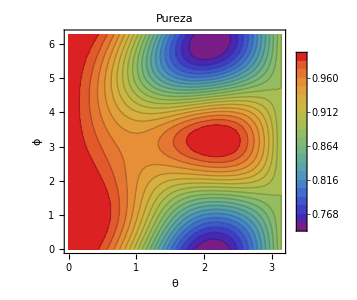

```mathematica
ContourPlot[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},PlotLabel->Style["Pureza",15,Bold,Black]]
```

Método numérico:

Se localizan los pares de valores {θ, ϕ} en donde la pureza es máxima y el valor de la misma.

```mathematica
maximos=MaximumPurity[v1,v2]
```

{{{0.247481,0.977489},{2.17375,3.18024}},1.}

Gráficas con los máximos (puntos blancos).

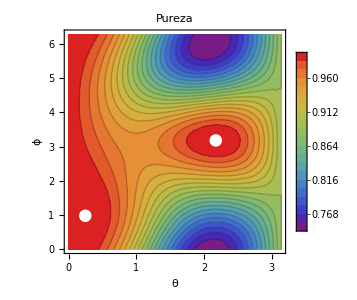

```mathematica
ContourPlot[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},Epilog->{White,PointSize[0.03],Point[maximos[[1]]]},PlotLabel->Style["Pureza",15,Bold,Black]]
```

Es de interés ubicar los valores donde γ_A=1, por lo que puede verificarse al sustituir los  pares de θ  y  ϕ  encontrados.

```mathematica
PurityOfSubsystemA[v1,v2,maximos[[1,1,1]],maximos[[1,1,2]]]
PurityOfSubsystemA[v1,v2,maximos[[1,2,1]],maximos[[1,2,2]]]
```

1.

1.

Al sustituir los valores de θ y ϕ , se obtienen a los estados separables de 2 qubits.

```mathematica
Cos[maximos[[1,1,1]]/2] v1+Exp[I maximos[[1,1,2]]] Sin[maximos[[1,1,1]]/2] v2
Cos[maximos[[1,2,1]]/2] v1+Exp[I maximos[[1,2,2]]] Sin[maximos[[1,2,1]]/2] v2
```

{0.331156+0.373946 ⅈ,-0.0935343+0.509596 ⅈ,0.218847+0.429331 ⅈ,-0.210595+0.453315 ⅈ}

{0.726418+0.0836727 ⅈ,-0.628187-0.0353423 ⅈ,0.194898+0.0437995 ⅈ,-0.169616-0.0278216 ⅈ}

Método analítico:

Encuentra a los coeficientes A y B asociados a los estados separables, usando la ecuación 2.30 del trabajo de tesis.

```mathematica
Take[AnalyticalSeparableStates[v1,v2],2]
```

{{0.992354,0.0690077+0.102331 ⅈ},{0.465255,-0.884516-0.0342038 ⅈ}}

Estados separables correspondientes a los coeficientes A y B.

```mathematica
AnalyticalSeparableStates[v1,v2][[3]]
```

{{0.331156+0.373946 ⅈ,-0.0935343+0.509596 ⅈ,0.218847+0.429331 ⅈ,-0.210595+0.453315 ⅈ},{0.726418+0.0836727 ⅈ,-0.628187-0.0353423 ⅈ,0.194898+0.0437995 ⅈ,-0.169616-0.0278216 ⅈ}}

#### Estados de 1 qubit

Se encuentran a los estados de 1 qubit con el método y consideraciones descritas en la sección 2.5 del trabajo de tesis.

La primera sublista contiene a los estados ϕ_A y ϕ_B que componen al primer estado ψ_1= ϕ_A ϕ_B .
La segunda sublista contiene a los estados ϕ_A y ϕ_B que componen al primer estado ψ_2= ϕ_A ϕ_B .

```mathematica
Take[SeparableStatesWith1QStates[v1,v2],2]
```

{{{0.719678,0.67214+0.174045 ⅈ},{0.694059,0.44394+0.566744 ⅈ}},{{0.964652,0.262039+0.0279807 ⅈ},{0.758016,-0.651121+0.03812 ⅈ}}}

Estados ψ_1= ϕ_A ϕ_B  y ψ_2= ϕ_A ϕ_B .

```mathematica
Take[SeparableStatesWith1QStates[v1,v2],{3,4}]
```

{{0.499499,0.319494+0.407873 ⅈ,0.466505+0.120797 ⅈ,0.199751+0.458197 ⅈ},{0.731221,-0.628105+0.0367725 ⅈ,0.19863+0.0212099 ⅈ,-0.171686-0.00822995 ⅈ}}

Estados  K_1ψ_1=  ϕ_A ϕ_B  y  K_2ψ_2= ϕ_A ϕ_B .

```mathematica
SeparableStatesWith1QStates[v1,v2][[5]]
```

{{0.499499,0.319494+0.407873 ⅈ,0.466505+0.120797 ⅈ,0.199751+0.458197 ⅈ},{0.731221,-0.628105+0.0367725 ⅈ,0.19863+0.0212099 ⅈ,-0.171686-0.00822995 ⅈ}}

### Estados entrelazados

#### Funciones

Consultar la documentación de las funciones en la secciones 3.2  y 3.3 del trabajo de tesis.

```mathematica
Concurrence[v1_,v2_,θ_,ϕ_]:=Sqrt[2 Chop[(1-PurityOfSubsystemA[v1,v2,θ,ϕ])]]//Quiet

EntanglementEntropy[v1_,v2_,θ_,ϕ_]:=Module[{psi,rho,rhoA,eigenvalues},
psi=Cos[θ/2]*v1+Exp[I*ϕ]*Sin[θ/2] v2;(*estado en el subespacio generado por v1 y v2*)
rho=Transpose[{psi}].Conjugate[{psi}];(*Matriz densidad del sistema completo*)
rhoA=ReducedDensityMatrix[rho,{2}];(*Matriz densidad reducida*)
eigenvalues=Eigenvalues[rhoA];(*autovalores de rhoA*)(*{-N[Sum[eigenvalues[[i]] Log[eigenvalues[[i]]],{i,1,Dimensions[eigenvalues][[1]]}]],eigenvalues}*)-N[Sum[eigenvalues[[i]] Log[2,eigenvalues[[i]]],{i,1,Dimensions[eigenvalues][[1]]}]]]

MinimumPurity[v1_,v2_]:=Module[{M,dev,sol,d,data,secdθ,secdϕ,secdθϕ,delta,m,min,points,θ,ϕ},dev={FullSimplify[Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],θ],Element[{θ,ϕ},Reals]]],FullSimplify[Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],ϕ],Element[{θ,ϕ},Reals]]]};
M=NMinimize[{PurityOfSubsystemA[v1,v2,θ,ϕ],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]];
(*Busca los puntos {θ,ϕ} donde la derivada es cero empezando en {θ=θ0,ϕ=ϕ0}*)sol[θ0_,ϕ0_]:={θ,ϕ}/.FindRoot[{dev[[1]]==0,dev[[2]]==0},{θ,θ0,0,Pi},{ϕ,ϕ0,0,2 Pi}];
d=0.5;
data=Table[sol[θ0,ϕ0],{θ0,0,Pi,d},{ϕ0,0,2 Pi,0.5}]//Flatten[#,1]&//DeleteDuplicates@Chop[#]&//Quiet;(*Tabla con los valores {θ,ϕ} en donde la derivada es cero,para distintos puntos {θ0,ϕ0} de partida*)secdθ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,2}]];(*segunda derivada parcial en θ*)
secdϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{ϕ,2}]];(*segunda derivada parcial en ϕ*)
secdθϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,1},{ϕ,1}]];(*segunda derivada en θ,ϕ*)
delta[θ_,ϕ_]:=secdθ[θ,ϕ] secdϕ[θ,ϕ]-secdθϕ[θ,ϕ]^2;(*determinante de la matriz Jacobiana*)
m=Select[data,delta@@#>0&&secdθ@@#>0&];
(*Elimina puntos repetidos que tengan una diferencia menor a 10^-30*,Primer Intento*)
min=DeleteDuplicates[m,Norm[#1-#2]<10^-13&];
points=DeleteCases[min,{x_,y_}/;0==y||y==2 Pi||PurityOfSubsystemA[v1,v2,x,y]>M];
If[Length[points]>0,{points,PurityOfSubsystemA[v1,v2,points[[1,1]],points[[1,2]]]},{}]]

StatesWithConcurrenceC[C_,v1_,v2_,maximos_,minimos_]:=Module[{interpolacionpuntominimomaximo,λ,minimo,maximo,sol,data,Data},
interpolacionpuntominimomaximo[λ_,maximo_,minimo_]:=(1-λ) minimo+λ maximo;
sol[maximo_,minimo_]:=λ /.FindRoot[Concurrence[v1,v2,interpolacionpuntominimomaximo[λ,maximo,minimo][[1]],interpolacionpuntominimomaximo[λ,maximo,minimo][[2]]]==C, {λ, 0,1}]//Quiet; (*valor de λ asociado a una concurrencia C*)
data=Flatten[Table[interpolacionpuntominimomaximo[sol[minimos[[i]],maximos[[j]]],minimos[[i]],maximos[[j]]],{i,1,Length[minimos]},{j,1,Length[maximos]}],1]; (*valores de λ al tomar en cuenta todos los maximos y minimos*)
Data=DeleteCases[data, {x_, y_} /; NumberForm[Concurrence[v1, v2, x, y],{5,5}]  ≠NumberForm[C,{5,5}]];
Chop[DeleteDuplicates[Data, Norm[#1 - #2] < 10^-13 &] ,10^-7]
]
```

#### Exploración de subespacios

Con la base {v1,v2}, se visualiza a la concurrencia y entropía de entrelazamiento.

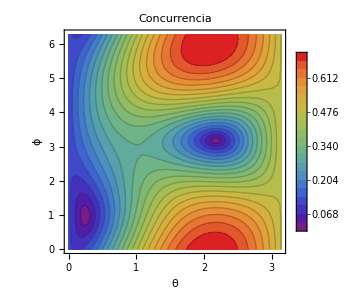

```mathematica
ContourPlot[Concurrence[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},PlotLabel->Style["Concurrencia",15,Bold,Black]]
```

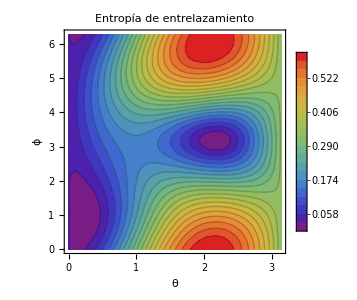

```mathematica
ContourPlot[EntanglementEntropy[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},PlotLabel->Style["Entropía de entrelazamiento",15,Bold,Black]]
```

#### Construcción de estados entrelazados

Como se ha descrito en el capítulo 3 del trabajo de tesis, el primer paso es conocer a la concurrencia máxima y mínima en el subespacio.

Por medio de los valores de {θ,ϕ} asociados a los máximos y mínimos de γ_A se obtiene a C_max y  C_min.

Ya se han calculado a {θ,ϕ}  de γ_Amax, pero falta encontrar a  {θ_min , ϕ_min }.

```mathematica
minimos=MinimumPurity[v1,v2]
```

{{{2.08821,6.03855}},0.740096}

Cálculo de C_max.

```mathematica
Concurrence[v1,v2,minimos[[1,1,1]],minimos[[1,1,2]]]
```

0.720978

Cálculo de C_min.

```mathematica
Concurrence[v1,v2,maximos[[1,1,1]],maximos[[1,1,2]]]
```

0

Hay que elegir un valor de C tal que C_min ≤ C ≤ C_max.

Valor de C seleccionado: 0.52 .

Algunos de los pares {θ, ϕ} asociados a esta concurrencia son :

```mathematica
states=StatesWithConcurrenceC[0.52,v1,v2,minimos[[1]],maximos[[1]]]
```

{{1.55116,4.56195},{2.1307,4.61856}}

Por lo que, los estados con esta concurrencia son :

```mathematica
psi=Table[Cos[states[[i,1]] /2] v1+Exp[I states[[i,2]]] Sin[states[[i,1]]/2] ,{ i, 1, Length[states] }]
```

{{0.174963-0.38599 ⅈ,-0.187267-0.38599 ⅈ,0.0699377-0.38599 ⅈ,-0.242782-0.38599 ⅈ},{0.107831-0.663444 ⅈ,-0.137809-0.663444 ⅈ,0.0366098-0.663444 ⅈ,-0.175455-0.663444 ⅈ}}

Gráficas con los estados obtenidos (puntos rojos).

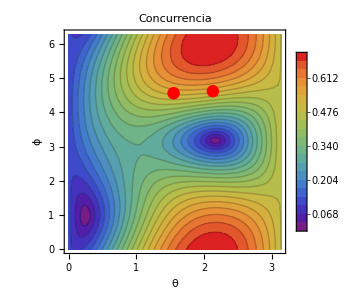

```mathematica
ContourPlot[Concurrence[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},Epilog->{Red,PointSize[0.03],Point[states]},PlotLabel->Style["Concurrencia",15,Bold,Black]]
```

## 3 y más qubits

### 3 qubits

#### Funciones

Consultar la documentación de las funciones y modificación de funciones anteriores en la sección 4.2 del trabajo de tesis.

```mathematica
PurityOfSubsystemA3Q[v1_,v2_,θ_,ϕ_]:=Module[{ψ,ρ,ρA},ψ=Cos[θ/2] v1+Exp[I ϕ] Sin[θ/2] v2;(*Construye el estado puro*)
ρ=Transpose[{ψ}].Conjugate[{ψ}];(*Matriz densidad del estado ψ*)
ρA=ReducedDensityMatrix[ρ,{2,3}];(*Matriz densidad reducida*)
Chop[FullSimplify[Tr[MatrixPower[ρA,2]],Element[{θ,ϕ},Reals]]] (*Pureza de ρA*)]

MaximumPurity3Q[v1_,v2_]:=Module[{M,dev,sol,d,data,secdθ,secdϕ,secdθϕ,delta,m,max,points,θ,ϕ},dev={FullSimplify[Evaluate[D[PurityOfSubsystemA3Q[v1,v2,θ,ϕ],θ],Element[{θ,ϕ},Reals]]],FullSimplify[Evaluate[D[PurityOfSubsystemA3Q[v1,v2,θ,ϕ],ϕ],Element[{θ,ϕ},Reals]]]};
M=NMaximize[{PurityOfSubsystemA3Q[v1,v2,θ,ϕ],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]];
(*Busca los puntos {θ,ϕ} donde la derivada es cero empezando en {θ=θ0,ϕ=ϕ0}*)sol[θ0_,ϕ0_]:={θ,ϕ}/.FindRoot[{dev[[1]]==0,dev[[2]]==0},{θ,θ0,0,Pi},{ϕ,ϕ0,0,2 Pi}];
d=0.5;
data=Table[sol[θ0,ϕ0],{θ0,0,Pi,d},{ϕ0,0,2 Pi,0.5}]//Flatten[#,1]&//DeleteDuplicates@Chop[#]&//Quiet;(*Tabla con los valores {θ,ϕ} en donde la derivada es cero,para distintos puntos {θ0,ϕ0} de partida*)secdθ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA3Q[v1,v2,θ,ϕ],{θ,2}]];(*segunda derivada parcial en θ*)
secdϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA3Q[v1,v2,θ,ϕ],{ϕ,2}]];(*segunda derivada parcial en ϕ*)
secdθϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA3Q[v1,v2,θ,ϕ],{θ,1},{ϕ,1}]];(*segunda derivada en θ,ϕ*)
delta[θ_,ϕ_]:=secdθ[θ,ϕ] secdϕ[θ,ϕ]-secdθϕ[θ,ϕ]^2;(*determinante de la matriz Jacobiana*)
m=Select[data,delta@@#>0&&secdθ@@#<0&];
(*Elimina puntos repetidos que tengan una diferencia menor a 10^-30*,Primer Intento*)
max=DeleteDuplicates[m,Norm[#1-#2]<10^-13&];
points=DeleteCases[max,{x_,y_}/;PurityOfSubsystemA3Q[v1,v2,x,y]<M];
If[Length[points]>0,{points,PurityOfSubsystemA3Q[v1,v2,points[[1,1]],points[[1,2]]]},{}]]

AnalyticalSeparableStates3Qubits[v1_,v2_]:=Module[{α0,α1,α2,α3,α4,α5,α6,α7,β0,β1,β2,β3,β4,β5,β6,β7,Ap1,Ap2,Ap3,Ap4,Ap5,Ap6,Bp1,Bp2,Bp3,Bp4,Bp5,Bp6,Cp1,Cp2,Cp3,Cp4,Cp5,Cp6,eq1,eq2,eq3,eq4,eq5,eq6,B,SOLT,SOLT1,SOL,SOL1,SOL2,SOL3,SOL4,SOL5,SOL6,Sol1,Sol2,Sol3,Sol4,Sol5,Sol6,A1,A2,B1,B2},α0=v1[[1]];
α1=v1[[2]];
α2=v1[[3]];
α3=v1[[4]];
α4=v1[[5]];
α5=v1[[6]];
α6=v1[[7]];
α7=v1[[8]];
β0=v2[[1]];
β1=v2[[2]];
β2=v2[[3]];
β3=v2[[4]];
β4=v2[[5]];
β5=v2[[6]];
β6=v2[[7]];
β7=v2[[8]];
Ap1=β0 β5-β1 β4;
Ap2=β0 β6-β2 β4;
Ap3=β0 β7-β3 β4;
Ap4=β1 β6-β2 β5;
Ap5=β1 β7-β3 β5;
Ap6=β2 β7-β3 β6;
Bp1=-(α0 β5+α5 β0-β1 α4-α1 β4);
Bp2=-(α0 β6+α6 β0-β2 α4-α2 β4);
Bp3=-(α0 β7+α7 β0-β3 α4-α3 β4);
Bp4=-(α1 β6+α6 β1-β2 α5-α2 β5);
Bp5=-(α1 β7+α7 β1-β3 α5-α3 β5);
Bp6=-(α2 β7+α7 β2-β3 α6-α3 β6);
Cp1=α0 α5-α1 α4;
Cp2=α0 α6-α2 α4;
Cp3=α0 α7-α3 α4;
Cp4=α1 α6-α2 α5;
Cp5=α1 α7-α3 α5;
Cp6=α2 α7-α3 α6;
eq1=Ap1 B^2+Bp1 B+Cp1;
eq2=Ap2 B^2+Bp2 B+Cp2;(*6 ecuaciones cuadráticas a resolver*)
eq3=Ap3 B^2+Bp3 B+Cp3;
eq4=Ap4 B^2+Bp4 B+Cp4;
eq5=Ap5 B^2+Bp5 B+Cp5;
eq6=Ap6 B^2+Bp6 B+Cp6;
SOL1=Solve[eq1==0,B]//Quiet;
Sol1=If[Length[SOL1[[1]]]>0,B/.SOL1,{}];
SOL2=Solve[eq2==0,B]//Quiet;
Sol2=If[Length[SOL2[[1]]]>0,B/.SOL2,{}];
SOL3=Solve[eq3==0,B]//Quiet;
Sol3=If[Length[SOL3[[1]]]>0,B/.SOL3,{}];
SOL4=Solve[eq4==0,B]//Quiet;
Sol4=If[Length[SOL4[[1]]]>0,B/.SOL4,{}];
SOL5=Solve[eq5==0,B]//Quiet;
Sol5=If[Length[SOL5[[1]]]>0,B/.SOL5,{}];
SOL6=Solve[eq6==0,B]//Quiet;
Sol6=If[Length[SOL6[[1]]]>0,B/.SOL6,{}];
SOLT={Sol1,Sol2,Sol3,Sol4,Sol5,Sol6};
SOLT1=DeleteCases[SOLT,x_/;Length[x]==0];
SOL=Intersection[##]&@@SOLT1;(*evalúa si las 6 ecuaciones comparten raíces*)
If[Length[SOL]==0,{},A1=1/Sqrt[1+Norm[SOL[[1]]]^2];
B1=SOL[[1]]/Sqrt[1+Norm[SOL[[1]]]^2];
A2=1/Sqrt[1+Norm[SOL[[2]]]^2];
B2=SOL[[2]]/Sqrt[1+Norm[SOL[[2]]]^2];
{{A1,B1},{A2,B2}}]]
```

#### Búsqueda de estados separables

De nuevo, lo primero es generar una base ortonormal, pero ahora para un sistema de 3 qubits:

```mathematica
Base=OrthonormalBasis[3];
v1=Base[[1]]
v2=Base[[2]]
```

{-0.0767899+0.30468 ⅈ,-0.199564+0.30468 ⅈ,-0.108579+0.30468 ⅈ,0.265065+0.30468 ⅈ,0.000136872+0.30468 ⅈ,-0.14334+0.30468 ⅈ,0.290823+0.30468 ⅈ,-0.156417+0.30468 ⅈ}

{-0.229727+0.112428 ⅈ,0.70962+0.123423 ⅈ,-0.250465+0.115275 ⅈ,-0.337522+0.0818135 ⅈ,-0.276068+0.105539 ⅈ,0.296182+0.118388 ⅈ,-0.0829339+0.0795067 ⅈ,0.0506934+0.119559 ⅈ}

La pureza γ_A se visualiza en un mapa de contorno (acá se considera que el sistema A está compuesto por 1 qubit y el sistema B por 2 qubits).

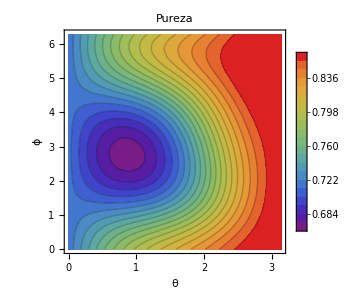

```mathematica
ContourPlot[PurityOfSubsystemA3Q[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},PlotLabel->Style["Pureza",15,Bold,Black]]
```

Método numérico:

Se localizan los pares de valores {θ, ϕ} en donde la pureza es máxima y el valor de la misma.

```mathematica
maximos=MaximumPurity3Q[v1,v2]
```

{{{2.85866,5.37534}},0.870867}

En este caso, la pureza máxima es 0.870867, por lo que no existen estados separables en el subespacio.

Método analítico:

Encuentra a los coeficientes A y B asociados a los estados separables (si existen), usando el método descrito en la sección 4.2 del trabajo de tesis.

```mathematica
AnalyticalSeparableStates3Qubits[v1,v2]
```

{}

El resultado coincide con el método numérico, ya que no se encontraron a los coeficientes A y B para este subespacio.

### 4 y más qubits

#### Funciones

Consultar la documentación de las funciones y modificación de funciones anteriores en la sección 4.2 del trabajo de tesis. Nota: NumQubitsB es el número de qubits en el sistema B.

```mathematica
PurityOfSubsystemABipartiteSystem[v1_,v2_,θ_,ϕ_,NumQubitsB_]:=Module[{n,ψ,ρ,ρA},n=Log[2,Dimensions[v1]][[1]];(*número de quits en el sistema completo*)
ψ=Cos[θ/2] v1+Exp[I ϕ] Sin[θ/2] v2;(*Construye el estado puro*)
ρ=Transpose[{ψ}].Conjugate[{ψ}];(*Matriz densidad del estado ψ*)
ρA=ReducedDensityMatrix[ρ,Take[Range[n],-NumQubitsB]];(*Matriz densidad reducida*)
Chop[FullSimplify[Tr[MatrixPower[ρA,2]],Element[{θ,ϕ},Reals]]] (*Pureza de ρA*)]


MaximumPurityBipartiteSystem[v1_,v2_,NumQubitsB_]:=Module[{M,dev,sol,d,data,secdθ,secdϕ,secdθϕ,delta,m,max,points,θ,ϕ},dev={FullSimplify[Evaluate[D[PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,NumQubitsB],θ],Element[{θ,ϕ},Reals]]],FullSimplify[Evaluate[D[PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,NumQubitsB],ϕ],Element[{θ,ϕ},Reals]]]};
M=NMaximize[{PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,NumQubitsB],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]];
(*Busca los puntos {θ,ϕ} donde la derivada es cero empezando en {θ=θ0,ϕ=ϕ0}*)sol[θ0_,ϕ0_]:={θ,ϕ}/.FindRoot[{dev[[1]]==0,dev[[2]]==0},{θ,θ0,0,Pi},{ϕ,ϕ0,0,2 Pi}];
d=0.5;
data=Table[sol[θ0,ϕ0],{θ0,0,Pi,d},{ϕ0,0,2 Pi,0.5}]//Flatten[#,1]&//DeleteDuplicates@Chop[#]&//Quiet;(*Tabla con los valores {θ,ϕ} en donde la derivada es cero,para distintos puntos {θ0,ϕ0} de partida*)secdθ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,NumQubitsB],{θ,2}]];(*segunda derivada parcial en θ*)
secdϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,NumQubitsB],{ϕ,2}]];(*segunda derivada parcial en ϕ*)
secdθϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,NumQubitsB],{θ,1},{ϕ,1}]];(*segunda derivada en θ,ϕ*)
delta[θ_,ϕ_]:=secdθ[θ,ϕ] secdϕ[θ,ϕ]-secdθϕ[θ,ϕ]^2;(*determinante de la matriz Jacobiana*)
m=Select[data,delta@@#>0&&secdθ@@#<0&];
(*Elimina puntos repetidos que tengan una diferencia menor a 10^-30*,Primer Intento*)
max=DeleteDuplicates[m,Norm[#1-#2]<10^-13&];
points=DeleteCases[max,{x_,y_}/;PurityOfSubsystemABipartiteSystem[v1,v2,x,y,NumQubitsB]<M];
If[Length[points]>0,{points,PurityOfSubsystemABipartiteSystem[v1,v2,points[[1,1]],points[[1,2]],NumQubitsB]},{}]]
```

#### Búsqueda de estados separables

Primero, hay que generar una base ortonormal para el número de qubits deseados. Se tomará un sistema de 4 qubits:

```mathematica
Base=OrthonormalBasis[4];
v1=Base[[1]]
v2=Base[[2]]
```

{-0.015164+0.217908 ⅈ,-0.0187946+0.217908 ⅈ,0.108163+0.217908 ⅈ,-0.139398+0.217908 ⅈ,-0.0938583+0.217908 ⅈ,0.157463+0.217908 ⅈ,0.133815+0.217908 ⅈ,-0.0486235+0.217908 ⅈ,-0.169332+0.217908 ⅈ,0.040532+0.217908 ⅈ,0.11151+0.217908 ⅈ,-0.0634073+0.217908 ⅈ,0.122943+0.217908 ⅈ,0.213297+0.217908 ⅈ,-0.0525409+0.217908 ⅈ,0.211007+0.217908 ⅈ}

{-0.152401+0.077524 ⅈ,-0.198169+0.0776629 ⅈ,0.176494+0.0728063 ⅈ,0.44568+0.0822764 ⅈ,0.042456+0.0805343 ⅈ,-0.195184+0.0709204 ⅈ,0.0438158+0.071825 ⅈ,0.317964+0.0788039 ⅈ,0.426914+0.0834215 ⅈ,0.24623+0.0753934 ⅈ,-0.192925+0.0726783 ⅈ,-0.0937407+0.0793695 ⅈ,-0.24024+0.0722409 ⅈ,-0.333513+0.0687846 ⅈ,-0.111859+0.0789538 ⅈ,-0.0479931+0.0688722 ⅈ}

Lo siguiente, será elegir el número de qubits que habrá en el sistema B. Se va a considerar que el sistema B está compuesto por 2 qubits.

La pureza γ_A se visualiza en un mapa de contorno.

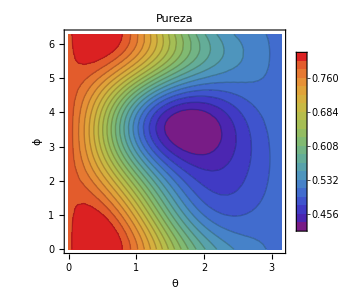

```mathematica
ContourPlot[PurityOfSubsystemABipartiteSystem[v1,v2,θ,ϕ,2],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ",17,Bold,Black],Style["ϕ",17,Bold,Black]},PlotLabel->Style["Pureza",15,Bold,Black]]
```

Se localizan los pares de valores {θ, ϕ} en donde la pureza es máxima y el valor de la misma.

```mathematica
maximos=MaximumPurityBipartiteSystem[v1,v2,2]
```

{{{0.411763,0.14223}},0.825954}

En este caso, la pureza máxima es 0.825954, por lo que no existen estados separables en el subespacio.

Para 4 y más qubits, aún no se cuenta con un método analítico para comparar debido a su complejidad.